ПРИЛОЖЕНИЕ А
Решение уравнения Рикатти

```mathematica
A=({{-1, -1}, {0, 1}});
b=({{0, 1}});
B=Transpose@b;
Q=({{5, 5}, {5, 5}});
R=IdentityMatrix[1];
P=RiccatiSolve[1.0{A,B},{Q,R}];
MatrixForm@P
```

(2. | 1.
1. | 3.)

```mathematica
Subscript[k, opt]=b.P
```

{{1.,3.}}

```mathematica
X=Transpose@{{Subscript[x, 1],Subscript[x, 2]}};
U=-Subscript[k, opt].X//First
```

{-1. x_1-3. x_2}

```mathematica
Det@P
```

5.

ПРИЛОЖЕНИЕ Б
Компьютерное моделирование

```mathematica
x={x1[t],x2[t]};
xE={xE1[t],xE2[t]};
A={{-1,-1},{0,1}};
b={0,1};
c={1,1};
y=c.x
Kmod={0,2};
Kopt={1,3};
L={-2,3};
```

x1[t]+x2[t]

Уравнения объекта и наблюдателя, закон управления:

```mathematica
u=-Kmod.x(*-Kmod.xE+Sin[t]*)
uE = -Kmod.xE
uOpt=-Kopt.x
EqPlant=D[x,t]-(A.x + b u)
EqPlant1 = D[x,t]-(A.x + b uE)
EqObs=D[xE,t]-(A.xE+b u+L (y-c.xE))
EqObs1=D[xE,t]-(A.xE+b uE+L (y-c.xE))
EqOpt=D[x,t]-(A.x + b uOpt)
```

-2 x2[t]

-2 xE2[t]

-x1[t]-3 x2[t]

{x1[t]+x2[t]+x1'[t],x2[t]+x2'[t]}

{x1[t]+x2[t]+x1'[t],-x2[t]+2 xE2[t]+x2'[t]}

{xE1[t]+2 (x1[t]+x2[t]-xE1[t]-xE2[t])+xE2[t]+xE1'[t],2 x2[t]-3 (x1[t]+x2[t]-xE1[t]-xE2[t])-xE2[t]+xE2'[t]}

{xE1[t]+2 (x1[t]+x2[t]-xE1[t]-xE2[t])+xE2[t]+xE1'[t],-3 (x1[t]+x2[t]-xE1[t]-xE2[t])+xE2[t]+xE2'[t]}

{x1[t]+x2[t]+x1'[t],x1[t]+2 x2[t]+x2'[t]}

Моделирование(решение задачи модульного управления с ассимптотическим наблюдателем):

```mathematica
tf=12.0;
slv=NDSolve[{
EqPlant[[1]]==0,EqPlant[[2]]==0,
x1[0]==1.0,x2[0]==-1.0,
EqObs[[1]]==0,EqObs[[2]]==0,
xE1[0]==0,xE2[0]==0
},{x1,x2,xE1,xE2},{t,0,tf}][[1]];
slv1=NDSolve[{
EqPlant1[[1]]==0,EqPlant1[[2]]==0,
x1[0]==1.0,x2[0]==-1.0,
EqObs1[[1]]==0,EqObs1[[2]]==0,
xE1[0]==0,xE2[0]==0
},{x1,x2,xE1,xE2},{t,0,tf}][[1]];
slv2=NDSolve[{
EqOpt[[1]]==0,EqOpt[[2]]==0,
x1[0]==1.0,x2[0]==-1.0
},{x1,x2},{t,0,tf}][[1]];
```

Модальное управление:

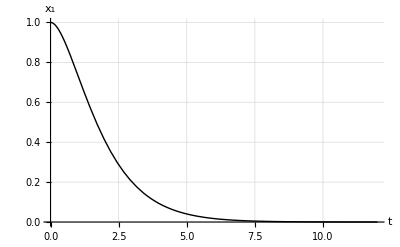

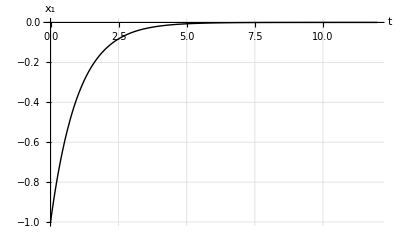

```mathematica
Plot[{x1[t]/.slv},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
```

J1 и J2

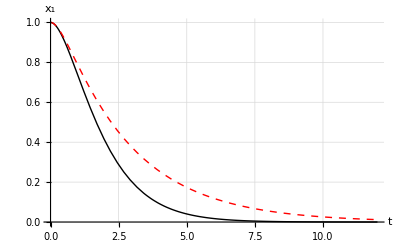

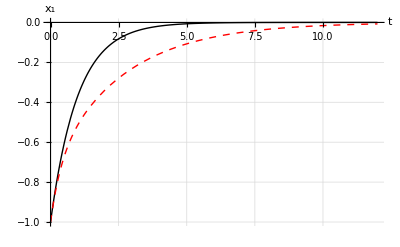

```mathematica
Plot[{x1[t]/.slv,x1[t]/.slv2},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv,x2[t]/.slv2},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
```

ЛКЗ J1 и наблюдатель

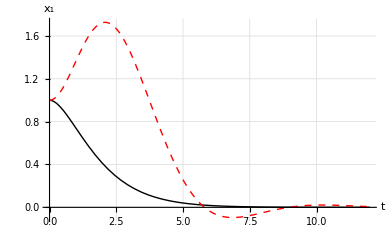

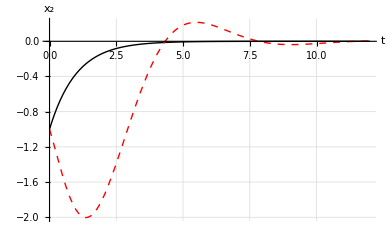

```mathematica
Plot[{x1[t]/.slv,x1[t]/.slv1},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_1"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
Plot[{x2[t]/.slv,x2[t]/.slv1},{t,0,tf},
PlotStyle->{{Black,Thick},{Red,Dashed,Thick}},
AxesLabel->{"t","x_2"},LabelStyle->{14,Black,FontFamily-> "Times"},
GridLines->Automatic,PlotRange->All]
```